# F[x]

```mathematica
orderFiles[dir_]:=Module[{filenames,order},
filenames=Import[dir];
order=Ordering@*Flatten@StringCases[filenames,x_~~y:DigitCharacter..~~".tif":> ToExpression@y];
filenames[[order]]
];
```

```mathematica
generateMesh[dir_String,voxelVol_]:=Module[{filenames,masks,im3d,morpComp,dim,dimtake,im3d2,mesh},
filenames=orderFiles[dir];
masks=Binarize@Import[dir<>#]&/@filenames;
im3d=Image3D@masks;
morpComp=MorphologicalComponents[im3d];
dim=First@ImageDimensions[im3d];
dimtake=MapAt[#-1&,
(MapAt[dim-#&,Reverse@Thread[Last@@ComponentMeasurements[morpComp,"BoundingBox"]],{2}]//Round)/. 0->1,{1,2}];
im3d2=Image3D[ImageTake[im3d,Sequence@@dimtake],BoxRatios->{1, 1, 1},ImageSize->Tiny];
Print[im3d2];
mesh=ImageMesh[im3d2,Method->"DualMarchingCubes",BoxRatios->{1, 1, 1},ImageSize->Tiny];
Print[{#,voxelVol*Abs@Volume[#]}&@mesh];
Print[{#,voxelVol*Abs[Volume[#]]}&@ImageMesh[GaussianFilter[im3d2,3],Method-> "DualMarchingCubes",BoxRatios->{1, 1, 1},ImageSize->Tiny]];
];
```

```mathematica
fitEllipsoid3D[image_Image3D]:=Block[{im,pixpos,meanpos,convexHull,mesh,points,minval,rules,ainv,centre,Σ,ellipsoidLJ,U,λ,U2},
im=image;
pixpos=PixelValuePositions[im,1];
meanpos=N@Mean[pixpos];
convexHull=ConvexHullMesh[#-meanpos&/@pixpos,BoxRatios->{1, 1, 1}];Print[mesh=DiscretizeRegion[convexHull,BoxRatios->{1, 1, 1},ImageSize->Tiny]];
points=MeshPrimitives[mesh,0]/.Point->Sequence;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[3]}];
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
ellipsoidLJ=Ellipsoid[centre,Σ];
Print@Graphics3D[{PointSize[0.01],Black,Point[points],Opacity[.2],Blue,ellipsoidLJ},
Axes->True,BoxRatios->{1,1,1},ImageSize->Medium];
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
];
```

```mathematica
fitEllipsoid3DAlt[image_Image3D]:=Block[{im,pixpos,meanpos,convexHull,mesh,points,minval,rules,ainv,centre,Σ,ellipsoidLJ,U,λ,U2},
im=image;
pixpos=PixelValuePositions[MorphologicalPerimeter@im,1];
meanpos=N@Mean[pixpos];
points=#-meanpos&/@pixpos;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[3]}];
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
ellipsoidLJ=Ellipsoid[centre,Σ];
Print@Graphics3D[{PointSize[0.01],Black,Point[points],Opacity[.2],Blue,ellipsoidLJ},
Axes->True,BoxRatios->{1,1,1},ImageSize->Medium];
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
];
```

# Test Data Vector

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@3D cell shape classifier\\@3D cell shape - test data\\";
```

#### cell 1

```mathematica
generateMesh[dir<>"ecadherin\\cell1\\", (Quantity[111.87, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{183.313,162.192,6.20656},{183.313,162.192,6.20656}}

```mathematica
classifier[<|"vol"->1384.2,"ellipse"->{183.3130492234697,162.1923751313349,6.206561873476615}*{111.87/1600,111.87/1600,1}|>]
```

Ecad

#### cell 2

```mathematica
generateMesh[dir<>"brachyury\\cell1\\", (Quantity[111.87, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{251.304,128.093,5.14617},{251.304,128.093,5.14617}}

```mathematica
classifier[<|"vol"->482.25,"ellipse"->{251.30389030011952,128.0934910586341,5.146169982167195}*{111.87/1600,111.87/1600,1}|>]
```

Brach

#### cell 3

```mathematica
generateMesh[dir<>"ecad brach\\cell1\\", (Quantity[111.87, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{234.312,177.128,6.17437},{234.312,177.128,6.17437}}

```mathematica
classifier[<|"vol"->851.28,"ellipse"->{234.31194057556513,177.12799474990013,6.1743740481221865}*{111.87/1600,111.87/1600,1}|>]
```

EB

#### cell 4

```mathematica
generateMesh[dir<>"brachyury\\cell2\\", (Quantity[111.87, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{224.527,139.997,4.61887},{224.527,139.997,4.61887}}

```mathematica
classifier[<|"vol"->345.32,"ellipse"->{224.52679772818024,139.99654240053934,4.6188711430161975}*{111.87/1600,111.87/1600,1}|>]
```

Brach

#### cell 5

```mathematica
generateMesh[dir<>"ecad brach\\cell2\\", (Quantity[111.87, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{202.577,194.98,9.28519},{202.577,194.98,9.28519}}

```mathematica
classifier[<|"vol"->1251.8,"ellipse"->{202.57709621392945,194.98007025252267,9.285193836612654}*{111.87/1600,111.87/1600,1}|>]
```

EB

#### cell 6

```mathematica
generateMesh[dir<>"ecad brach\\cell3\\", (Quantity[125.03, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{155.228,119.603,6.8191},{155.228,119.603,6.8191}}

```mathematica
classifier[<|"vol"->786.1,"ellipse"->{155.22758184870148,119.60298754550584,6.81909904029368}*{125.03/1600,125.03/1600,1}|>]
```

EB

#### cell 7

```mathematica
generateMesh[dir<>"brachyury\\cell3\\", (Quantity[125.03, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{133.83,88.3341,5.78925},{133.83,88.3341,5.78925}}

```mathematica
classifier[<|"vol"->435.63,"ellipse"->{133.83046271566937,88.3340586730523,5.789248919078985}*{125.03/1600,125.03/1600,1}|>]
```

Brach

#### cell 8

```mathematica
generateMesh[dir<>"brachyury\\cell4\\", (Quantity[118.08, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3DAlt[-Graphics3D-]
```

{{251.49,163.166,4.60321},{251.49,163.166,4.60321}}

```mathematica
classifier[<|"vol"->522.67,"ellipse"->{251.49018531011635,163.16616866498504,4.603207237538605}*{118.08/1600,118.08/1600,1}|>]
```

Brach

#### cell 9

```mathematica
generateMesh[dir<>"brachyury\\cell5\\", (Quantity[118.08, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{222.301,136.473,5.14898},{222.301,136.473,5.14898}}

```mathematica
classifier[<|"vol"->533.105,"ellipse"->{222.30105405877458,136.47276539128444,5.148978296849039}*{118.08/1600,118.08/1600,1}|>]
```

EB

#### cell 10

```mathematica
generateMesh[dir<>"ecadherin\\cell2\\", (Quantity[118.08, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{96.8341,88.5538,5.18135},{96.8341,88.5538,5.18135}}

```mathematica
classifier[<|"vol"->534.56,"ellipse"->{96.83414964480761,88.55384363256799,5.1813482445024555}*{118.08/1600,118.08/1600,1}|>]
```

Ecad

#### cell 11

```mathematica
generateMesh[dir<>"ecad brach\\cell4\\", (Quantity[118.08, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3DAlt[-Graphics3D-]
```

{{187.902,110.638,5.09936},{187.902,110.638,5.09936}}

```mathematica
classifier[<|"vol"->772.32,"ellipse"->{187.90238037644787,110.63847860953148,5.099363594178307}*{118.08/1600,118.08/1600,1}|>]
```

EB

#### cell 12

```mathematica
generateMesh[dir<>"ecad brach\\cell5\\", (Quantity[118.08, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{217.262,194.706,6.17782},{217.262,194.706,6.17782}}

```mathematica
classifier[<|"vol"->1116.46,"ellipse"->{217.2617472005414,194.70640200805283,6.1778238077537315}*{118.08/1600,118.08/1600,1}|>]
```

EB

#### cell 13

```mathematica
generateMesh[dir<>"ecadherin\\cell3\\", (Quantity[111.87, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{294.183,245.003,5.61402},{294.183,245.003,5.61402}}

```mathematica
classifier[<|"vol"->1219.82,"ellipse"->{294.18276332107683,245.00331100500813,5.614017589185559}*{111.87/1600,111.87/1600,1}|>]
```

EB

#### cell 14

```mathematica
generateMesh[dir<>"ecadherin\\cell4\\", (Quantity[132.84, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{148.66,140.779,5.17478},{148.66,140.779,5.17478}}

```mathematica
classifier[<|"vol"->795.40,"ellipse"->{148.65978592228643,140.7786014987723,5.174780266862946}*{132.84/1600,132.84/1600,1}|>]
```

EB

#### cell 15

```mathematica
generateMesh[dir<>"ecadherin\\cell5\\", (Quantity[132.84, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"]]
```

```mathematica
fitEllipsoid3D[-Graphics3D-]
```

{{145.561,133.836,4.64727},{145.561,133.836,4.64727}}

```mathematica
classifier[<|"vol"->607.05,"ellipse"->{145.5609210131126,133.83616835954862,4.647270880310492}*{132.84/1600,132.84/1600,1}|>]
```

EB

# Union Classifier

```mathematica
trainingdata={
<|"vol"->386.39,"ellipse"->{12.845025491481499,11.220072311290293,4.6501744374491585}|>->"Brach",<|"vol"->337.83,"ellipse"->{10.639136194777015,8.970740802891916,4.701291413492366}|>->"Brach",<|"vol"->321.31,"ellipse"->{12.102012023548829,7.592460281346914,4.165267584347247}|>->"Brach",<|"vol"->487.65,"ellipse"->{19.9735056825355,11.19537249895702,4.106391960438317}|>->"Brach",<|"vol"->1321.05,"ellipse"->{8.668254303834615,7.137949230000021,7.668601461745319}|>->"Ecad",<|"vol"->1924.66,"ellipse"->{17.504475789647824,16.56934839285648,8.29390476338982}|>->"Ecad",<|"vol"->677.53,"ellipse"->{13.494606623477832,11.218340563291054,5.161182557534426}|>->"EB",<|"vol"->1213.72,"ellipse"->{8.864623961136548,8.574781693610005,6.960821673633064}|>->"Ecad",<|"vol"->1148.42,"ellipse"->{11.63793565901513,10.705091547143473,6.180473356459843}|>->"Ecad",<|"vol"->972.11,"ellipse"->{18.151837164188443,10.448568771739325,6.7383599114673425}|>->"EB",<|"vol"->757.41,"ellipse"->{13.409080756620096,13.355099380366543,5.167403283295785}|>->"EB",<|"vol"->679.29,"ellipse"->{11.59043461737364,9.525040925532837,5.215534828364961}|>->"EB",<|"vol"->1104.55,"ellipse"->{13.21597487743128,11.960730047537657,6.787023267620833}|>->"EB",<|"vol"->934.12,"ellipse"->{21.572298639786982,15.869952233172915,5.122315071971005}|>->"EB",<|"vol"->1161.88,"ellipse"->{17.52445667641503,12.956910332557102,5.14782018934413}|>->"EB",<|"vol"->806.99,"ellipse"->{28.098536318501026,25.30257450733354,4.05356591754579}|>->"EB",
<|"vol"->311.1027867587147,"ellipse"->{9.98835692247164,4.366482067385957,3.7078273593279087}|>->"Brach",<|"vol"->336.41855603783534,"ellipse"->{20.957211416824656,4.298644566066125,2.7403909990176576}|>->"Brach",<|"vol"->256.70987175759495,"ellipse"->{4.288991193878235,2.893561000454337,4.935394559936162}|>->"Brach",<|"vol"->242.15118784116666,"ellipse"->{10.836750014794989,4.330802305065833,4.858656034871748}|>->"Brach",<|"vol"->247.69186022570162,"ellipse"->{27.22415703591735,9.021743431864058,4.1768140190330305}|>->"Brach",<|"vol"->299.6130660016753,"ellipse"->{8.841570923643465,4.886009516099131,4.694642731753038}|>->"Brach",<|"vol"->307.92701955814965,"ellipse"->{21.665260132957506,4.768876214473516,3.7348345506715863}|>->"Brach",<|"vol"->969.4581653236208,"ellipse"->{9.595068464839963,8.236709381602981,6.304789556303579}|>->"Ecad",<|"vol"->1134.8348700342035,"ellipse"->{11.486961174585705,10.901143163764306,7.366068165621642}|>->"Ecad",<|"vol"->895.0803849599641,"ellipse"->{7.770646571133821,7.353874155736802,6.610377453638059}|>->"Ecad",<|"vol"->1072.1794343900242,"ellipse"->{8.640558805968402,7.258534685466028,6.373946744149435}|>->"Ecad",<|"vol"->956.0003478352069,"ellipse"->{10.94678717894393,8.532260620558048,6.326913862217323}|>->"Ecad",<|"vol"->953.6444227217423,"ellipse"->{8.945056398466866,7.986278572624707,6.96154931260259}|>->"Ecad",<|"vol"->829.9819519822719,"ellipse"->{9.457601788402746,6.678137653425736,5.959088082754337}|>->"Ecad",<|"vol"->1373.9979242686177,"ellipse"->{9.075304985598196,6.999351307100153,6.511188146427696}|>->"Ecad",<|"vol"->1251.855005629671,"ellipse"->{11.120960275039598,8.57776202453194,6.278911187677796}|>->"Ecad"
};
```

```mathematica
Options[Classify]
```

{BatchProcessing→Automatic,DistributionPostProcessing→Automatic,FeatureWeights→Automatic,ImputeMissingValues→True,PredictionName→Automatic,ProcessorCaching→True,RecordLog→True,TieBreakerFunction→RandomChoice,TrainingSizeRatio→Automatic,ClassPriors→Automatic,FeatureExtractor→Identity,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,Method→Automatic,NominalVariables→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234,TargetDevice→CPU,TimeGoal→Automatic,TrainingProgressCheckpointing→None,TrainingProgressReporting→Automatic,UtilityFunction→Automatic,ValidationSet→Automatic,Weights→Automatic}

```mathematica
classifier=Classify[trainingdata,Method->"NeuralNetwork",TargetDevice->"GPU",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
Information[classifier]
```

Classifier information
Data type | {Numerical,NumericalVector (3)}
Classes | ,,BrachEBEcad
Accuracy | (76.27.) %
Method | NeuralNetwork
Single evaluation time | 3.99 ms/example
Batch evaluation speed | 31.8 examples/ms
Loss | 0.907 ± 0.69
Model memory | 250. kB
Training examples used | 32 examples
Training time | 22.5 s

```mathematica
Through[{Counts@Apply[SameQ,#,{1}]&,#&}[Thread[{classifier@Keys@trainingdata,Values@trainingdata}]]]
```

{<|True→31,False→1|>,{{Brach,Brach},{Brach,Brach},{Brach,Brach},{Brach,Brach},{Ecad,Ecad},{EB,Ecad},{EB,EB},{Ecad,Ecad},{Ecad,Ecad},{EB,EB},{EB,EB},{EB,EB},{EB,EB},{EB,EB},{EB,EB},{EB,EB},{Brach,Brach},{Brach,Brach},{Brach,Brach},{Brach,Brach},{Brach,Brach},{Brach,Brach},{Brach,Brach},{Ecad,Ecad},{Ecad,Ecad},{Ecad,Ecad},{Ecad,Ecad},{Ecad,Ecad},{Ecad,Ecad},{Ecad,Ecad},{Ecad,Ecad},{Ecad,Ecad}}}

```mathematica
testingData={
<|"vol"->1384.2,"ellipse"->{183.3130492234697,162.1923751313349,6.206561873476615}*{111.87/1600,111.87/1600,1}|>->"Ecad",
<|"vol"->482.2,"ellipse"->{251.30389030011952,128.0934910586341,5.146169982167195}*{111.87/1600,111.87/1600,1}|>->"Brach",
<|"vol"->851.28,"ellipse"->{234.31194057556513,177.12799474990013,6.1743740481221865}*{111.87/1600,111.87/1600,1}|>->"EB",
<|"vol"->345.32,"ellipse"->{224.52679772818024,139.99654240053934,4.6188711430161975}*{111.87/1600,111.87/1600,1}|>->"Brach",
<|"vol"->1251.8,"ellipse"->{202.57709621392945,194.98007025252267,9.285193836612654}*{111.87/1600,111.87/1600,1}|>->"EB",
<|"vol"->786.1,"ellipse"->{155.22758184870148,119.60298754550584,6.81909904029368}*{125.03/1600,125.03/1600,1}|> ->"EB",
<|"vol"->435.63,"ellipse"->{133.83046271566937,88.3340586730523,5.789248919078985}*{125.03/1600,125.03/1600,1}|>->"Brach",
<|"vol"->522.67,"ellipse"->{251.49018531011635,163.16616866498504,4.603207237538605}*{118.08/1600,118.08/1600,1}|>->"Brach",
<|"vol"->533.105,"ellipse"->{222.30105405877458,136.47276539128444,5.148978296849039}*{118.08/1600,118.08/1600,1}|>->"Brach",
<|"vol"->534.56,"ellipse"->{96.83414964480761,88.55384363256799,5.1813482445024555}*{118.08/1600,118.08/1600,1}|>->"Ecad",
<|"vol"->772.32,"ellipse"->{187.90238037644787,110.63847860953148,5.099363594178307}*{118.08/1600,118.08/1600,1}|>->"EB",
<|"vol"->1116.46,"ellipse"->{217.2617472005414,194.70640200805283,6.1778238077537315}*{118.08/1600,118.08/1600,1}|>->"EB",
<|"vol"->1219.82,"ellipse"->{294.18276332107683,245.00331100500813,5.614017589185559}*{111.87/1600,111.87/1600,1}|>-> "Ecad",
<|"vol"->795.40,"ellipse"->{148.65978592228643,140.7786014987723,5.174780266862946}*{132.84/1600,132.84/1600,1}|>-> "Ecad"
};
```

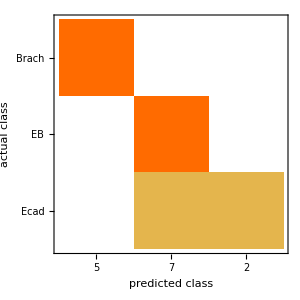
Classifier Measurements
Number of test examples | 14
Accuracy | (86.10.) %
Accuracy baseline | (36.13.) %
Geometric mean of probabilities | 0.048 ± 0.22
Mean cross entropy | 3.04 ± 2.2
Single evaluation time | 5.03 ms/example
Batch evaluation speed | 3.23 examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
ClassifierMeasurements[classifier,testingData,"Report"]
```

```mathematica
ClassifierMeasurements[classifier,testingData,"Accuracy"]
```

0.857143

```mathematica
pp=RandomSample@Cases[
MapAt[List@@#&,Apply[Rule]/@trainingdata,{All,1}],HoldPattern[x_->y:"Ecad"|"Brach"|"EB"]:>
Which[y=="Ecad", Style[Callout[x,y],Red],y=="Brach", Style[Callout[x,y],Blue],True,
Style[Callout[x,y],Green]]
];
```

```mathematica
appendentry=Cases[{<|"vol"->1219.82,"ellipse"->{294.18276332107683,245.00331100500813,5.614017589185559}*{111.87/1600,111.87/1600,1}|>-> "Ecad",<|"vol"->795.40,"ellipse"->{148.65978592228643,140.7786014987723,5.174780266862946}*{132.84/1600,132.84/1600,1}|>-> "Ecad"},
PatternSequence[<|p_,q_|>-> r_]:>Style[Callout[{Last@p,Last@q},r],Black],{1}]
```

{Callout[{1219.82,{20.5689,17.1303,5.61402}},Ecad],Callout[{795.4,{12.3425,11.6881,5.17478}},Ecad]}

```mathematica
FeatureSpacePlot[Join[pp,appendentry],Method->"PrincipalComponentsAnalysis",
FeatureExtractor->"DimensionReducedVector",PlotStyle->Directive[Opacity[0.3],PointSize[0.04]],
ImageSize->Medium,Frame->True]
```

-Graphics-